```mathematica
Fitting the copula
```

Idea: Fit copula according to copula dependence measures, such as Spearman’s rho (rank correlation), Kendalls’ tau and quantile dependence, see e.g. Oh and Patton (2013) (screenshot below). This method is called “method of moments” in the literature. See also McNeil et al. (2005), Section 5.5. Note also the empirical DF variant, which ensures that the data lie strictly in the interior of the unit cube (page 232 of McNeil et al, 2005). See also Nelsen (2006). See Fermanian et al. (2004) for convergence of the sample measures to their population counterparts. 

Possibly use the following dependence measures for calibration: rank correlation, 0.05, 0.1, 0.9, 0.95 quantile dependence (this is what Oh and Patton (2013) use). 

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[α,β,μ,δ,μ1,μ2,δ1,δ2]
```

Density function

```mathematica
q[x_]:=√(1+x^2);
g[x_,α_,β_,μ_,δ_]:=(α Exp[δ √(α^2-β^2)-β μ] BesselK[1,δ α q[(x-μ)/δ]] Exp[β x])/(π q[(x-μ)/δ]);
```

Moment-generating function

```mathematica
M[u_,α_,β_,μ_,δ_]:=Exp[δ (√(α^2-β^2)-√(α^2-(β+u)^2))+μ u]
```

Standardize NIG PDF’s by setting location and scale

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=(α^2-β^2)^(3/2)/α^2 
μs[α_,β_]:=-(δs[α,β] β)/(√(α^2-β^2))
```

The NIG is implemented in Mathematica as a Generalised Hyperbolic distribution

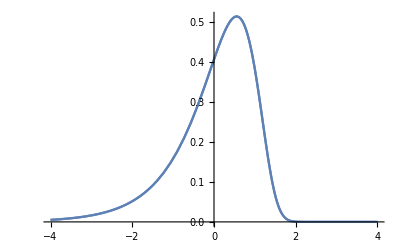
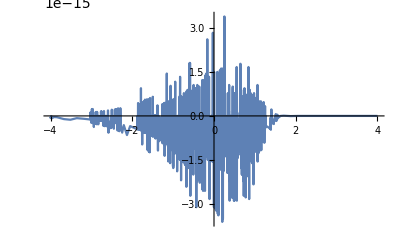

```mathematica
{Plot[{g[x,α,β,μs[α,β],δs[α,β]],PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]}/.{α->10, β->-9}, {x,-4,4},PlotRange->All],
Plot[{g[x,α,β,μs[α,β],δs[α,β]]-PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]}/.{α->10, β->-9}, {x,-4,4},PlotRange->All]
}
```

NIG factor copula
-Graphics-

```mathematica
NIGInv[p_,α_,β_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]
NIGCDF[x_,α_,β_]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[x_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
```

```mathematica
F2NIG[x_,y_,α_,β_,μ1_,μ2_,δ_,δ1_,δ2_]:=
NIntegrate[FNIG[x-z,α,β,μ1,δ1] FNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

### Copula dependence measures

Empirical DF

```mathematica
hatF[x_,s_]:=Module[{n},
n=Length[s];
1/(n+1) Length[Select[s, #1≤x&]]
]
```

NIG factor copula
-Graphics-
-Graphics-

```mathematica
Timing[FNIG[0.5,5,0.1,0,0.5]]
```

{0.032439,0.942472}

```mathematica
Timing[fNIG[0.5,5,0.1,0,0.5]]
```

{0.000918,0.307374}

```mathematica
Timing[F2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{5.49154,0.547637}

```mathematica
CNIG[u_,v_,α_,β_,δ_]:=F2NIG[NIGInv[u,α,β],NIGInv[v,α,β],α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ]
```

```mathematica
Timing[CNIG[0.5,0.1,5,0,1]]
```

{3.98152,0.0638757}

Spearman’s Rho
-Graphics-

```mathematica
Rho[α_,β_,δ_]:=
12 NIntegrate[CNIG[u,v,α,β,δ], {u,0,1}, {v,0,1}]-3
```

```mathematica
Rho[α_,β_,δ_]:=Module[{},
12 NIntegrate[FNIG[InvFNIG[u,α,β,μs[α,β],δs[α,β]]-z,α,β,μs[α,β],δs[α,β]-δ] FNIG[InvFNIG[v,α,β,μs[α,β],δs[α,β]]-z,α,β,μs[α,β],δs[α,β]-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞}, {u,0,1}, {v,0,1}]-3
]
```

```mathematica
Rho[α_,β_,δ_]:=Module[{μ1,δ1},
μ1=μs[α,β];
δ1=δs[α,β];
12NIntegrate[FNIG[NIGInv[u,α,β]-z,α,β,μ1,δ1-δ] FNIG[NIGInv[v,α,β]-z,α,β,μ1,δ1-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞},{u,0,0.5}, {v,0,0.5},PrecisionGoal->2] \
+ NIntegrate[FNIG[NIGInv[u,α,β]-z,α,β,μ1,δ1-δ] FNIG[NIGInv[v,α,β]-z,α,β,μ1,δ1-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞},{u,0.5,1.}, {v,0,0.5},PrecisionGoal->2] \
+  NIntegrate[FNIG[NIGInv[u,α,β]-z,α,β,μ1,δ1-δ] FNIG[NIGInv[v,α,β]-z,α,β,μ1,δ1-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞},{u,0,0.5}, {v,0.5,1.},PrecisionGoal->2] \
  + NIntegrate[FNIG[NIGInv[u,α,β]-z,α,β,μ1,δ1-δ] FNIG[NIGInv[v,α,β]-z,α,β,μ1,δ1-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞},{u,0.5,1.}, {v,0.5,1.},PrecisionGoal->2]-3
]
```

```mathematica
Clear[u]; Clear[v];
```

```mathematica
Timing[Rho[5,0,4]]
```

{121.648,0.0000202787}

```mathematica
α=2; 
β=1;
δ=0.5;
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
n=10000;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
```

```mathematica
{Mean[X1],Mean[X2]}
{Variance[X1], Variance[X2]}
```

{0.00340679,0.00398779}

{1.00878,1.02964}

```mathematica
{δ/δs[α,β],Correlation[X1,X2],(6 ArcSin[δ/(2 δs[α,β])])/π,(6 ArcSin[1/2 Correlation[X1,X2]])/π,SpearmanRho[X1,X2]}
```

{0.3849,0.392945,0.36986,0.377692,0.367439}

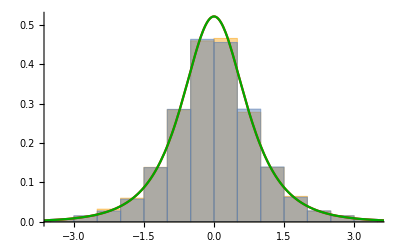

```mathematica
Show[
Histogram[{X1,X2}, Automatic, "PDF"],
Plot[{fNIG[x,α,β, μs[α,β], δs[α,β]],NIGPDF[x,α,β]}, {x,-4,4},PlotStyle->{Red,Darker[Green]}]
]
```

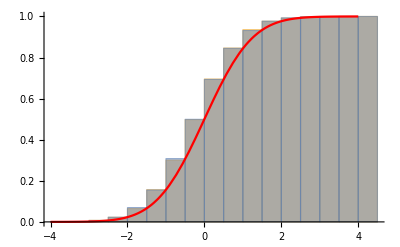

```mathematica
Show[
Histogram[{X1,X2}, Automatic, "CDF"],
Plot[FNIG[x,α,β, μs[α,β], δs[α,β]], {x,-4,4},PlotStyle->Red]
]
```

```mathematica
NIGInv[p_,α_,β_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]
NIGCDF[x_,α_,β_]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
Dynamic[k]
```

```mathematica
u1=Table[FNIG[X1[[k]],α,β,μs[α,β], δs[α,β]], {k,1,Length[X1]}];
```

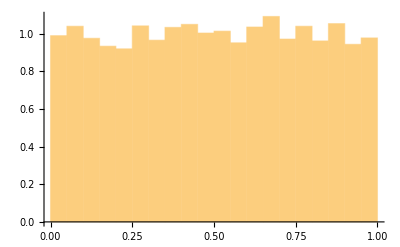

```mathematica
Histogram[u1, Automatic, "PDF"]
```

```mathematica
U=RandomVariate[UniformDistribution[],5000];
N1=Table[InvFNIG[U⟦k⟧,α,β,μs[α,β],δs[α,β]],{k,1,Length[U]}];
```

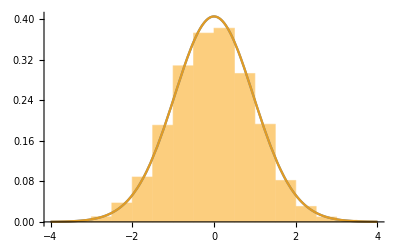

```mathematica
Show[
Histogram[N1, Automatic, "PDF"],
Plot[{fNIG[x, α, β, μs[α,β], δs[α,β]],NIGPDF[x,α,β]}, {x,-4,4}]
]
```

```mathematica
{F2NIG[1,1,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ],N[Length[Select[Transpose[{X1,X2}],#1⟦1⟧<1&&#1⟦2⟧<1&]]/Length[X1]]}
```

{0.783997,0.7875}

```mathematica
{F2NIG[0.5,1,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ],N[Length[Select[Transpose[{X1,X2}],#1⟦1⟧<0.5&&#1⟦2⟧<1&]]/Length[X1]]}
```

{0.670733,0.6727}

```mathematica
{F2NIG[-0.5,1,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ],N[Length[Select[Transpose[{X1,X2}],#1⟦1⟧<-0.5&&#1⟦2⟧<1&]]/Length[X1]]}
```

{0.305135,0.2995}

```mathematica
{F2NIG[0.5,0.25,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ],N[Length[Select[Transpose[{X1,X2}],#1⟦1⟧<0.5&&#1⟦2⟧<0.25&]]/Length[X1]]}
```

{0.545333,0.5434}

```mathematica
Timing[CNIG[0.5,0.1,α,β,δ]]
```

{6.28781,0.0979467}

```mathematica
x1=NIGInv[0.5,α,β];
x2=NIGInv[0.1,α,β];
N[1/Length[X1] Length[Select[Transpose[{X1,X2}],#1⟦1⟧<x1&&#1⟦2⟧<x2&]]]
```

0.0989

```mathematica
Table[CNIG[u,v, α, β, δ], {u,0.45, 0.55, 0.05}, {v,0.45, 0.55, 0.05}]
```

(0.349051 | 0.37149 | 0.390569
0.37149 | 0.398212 | 0.42149
0.390569 | 0.42149 | 0.449051)

```mathematica
CNIG[u_,v_,α_,β_,δ_]:=F2NIG[NIGInv[u,α,β],NIGInv[v,α,β],α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ]
```

```mathematica
Timing[NIntegrate[FNIG[NIGInv[u,α,β]-z,α,β,μs[α,β],δs[α,β]-δ] FNIG[NIGInv[v,α,β]-z,α,β,μs[α,β],δs[α,β]-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞}, {u,0.45,0.55}, {v,0.45,0.55}]]
```

{182.691,0.00397068}

```mathematica
Timing[NIntegrate[FNIG[NIGInv[u,α,β]-z,α,β,μs[α,β],δs[α,β]-δ] FNIG[NIGInv[v,α,β]-z,α,β,μs[α,β],δs[α,β]-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞}, {u,0.25,0.55}, {v,0.45,0.55}]]
```

{336.058,0.0100775}

```mathematica
Rho[α_,β_,δ_]:=Module[{},
12 NIntegrate[FNIG[InvFNIG[u,α,β,μs[α,β],δs[α,β]]-z,α,β,μs[α,β],δs[α,β]-δ] FNIG[InvFNIG[v,α,β,μs[α,β],δs[α,β]]-z,α,β,μs[α,β],δs[α,β]-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞}, {u,0,1}, {v,0,1}]-3
]
```

```mathematica
Timing[NIntegrate[NIGInv[u, 5, 0], {u,0,0.5}, PrecisionGoal->2]]
```

{0.29249,-0.396495}

```mathematica
Timing[NIntegrate[NIGInv[u, 5, 0], {u,0.9,1.0}, PrecisionGoal->2]]
```

{0.233169,0.175941}

```mathematica
Timing[NIntegrate[NIGInv[u, 5, 0], {u,0,0.5}, PrecisionGoal->2]+NIntegrate[NIGInv[u, 5, 0], {u,0.5,1}, PrecisionGoal->2]]
```

{0.50885,-1.11022×10^-16}

```mathematica
Timing[NIntegrate[NIGInv[u, 5, 0], {u,0, 0.2}]]
```

{15.8985,-0.279554}

```mathematica
Timing[Table[NIGInv[u, 5, 0], {u,0,1,0.005}]]
```

{3.98745,{-∞,-2.6207,-2.35331,-2.18794,-2.06579,-1.96791,-1.88566,-1.81438,-1.75123,-1.69436,-1.6425,-1.59474,-1.55038,-1.50891,-1.46991,-1.43306,-1.39808,-1.36477,-1.33294,-1.30243,-1.27311,-1.24488,-1.21763,-1.19128,-1.16575,-1.14099,-1.11692,-1.09351,-1.0707,-1.04846,-1.02674,-1.00551,-0.984744,-0.964408,-0.944479,-0.924933,-0.905749,-0.886906,-0.868386,-0.850172,-0.832247,-0.814598,-0.797211,-0.780072,-0.76317,-0.746493,-0.730031,-0.713774,-0.697713,-0.681838,-0.666142,-0.650617,-0.635254,-0.620048,-0.604991,-0.590077,-0.5753,-0.560654,-0.546134,-0.531734,-0.517449,-0.503275,-0.489207,-0.47524,-0.46137,-0.447594,-0.433906,-0.420304,-0.406784,-0.393342,-0.379974,-0.366678,-0.35345,-0.340287,-0.327187,-0.314145,-0.30116,-0.288228,-0.275347,-0.262514,-0.249727,-0.236983,-0.22428,-0.211615,-0.198986,-0.18639,-0.173826,-0.16129,-0.148782,-0.136298,-0.123836,-0.111395,-0.0989721,-0.0865654,-0.0741728,-0.0617923,-0.0494218,-0.0370594,-0.0247029,-0.0123505,-1.67418×10^-14,0.0123505,0.0247029,0.0370594,0.0494218,0.0617923,0.0741728,0.0865654,0.0989721,0.111395,0.123836,0.136298,0.148782,0.16129,0.173826,0.18639,0.198986,0.211615,0.22428,0.236983,0.249727,0.262514,0.275347,0.288228,0.30116,0.314145,0.327187,0.340287,0.35345,0.366678,0.379974,0.393342,0.406784,0.420304,0.433906,0.447594,0.46137,0.47524,0.489207,0.503275,0.517449,0.531734,0.546134,0.560654,0.5753,0.590077,0.604991,0.620048,0.635254,0.650617,0.666142,0.681838,0.697713,0.713774,0.730031,0.746493,0.76317,0.780072,0.797211,0.814598,0.832247,0.850172,0.868386,0.886906,0.905749,0.924933,0.944479,0.964408,0.984744,1.00551,1.02674,1.04846,1.0707,1.09351,1.11692,1.14099,1.16575,1.19128,1.21763,1.24488,1.27311,1.30243,1.33294,1.36477,1.39808,1.43306,1.46991,1.50891,1.55038,1.59474,1.6425,1.69436,1.75123,1.81438,1.88566,1.96791,2.06579,2.18794,2.35331,2.6207,∞}}

```mathematica
Timing[CNIG[u,v,5,0,1]]
```

{4.56855,0.12228}

### Read BTC data

```mathematica
data=Import[NotebookDirectory[]<> "../processed_data/btc_future_crix.csv"];
```

```mathematica
Dimensions[data]
```

{646,14}

```mathematica
data[[1;;10,12;;13]]
```

(return_btc | return_brr
-0.0226425 | -0.0564519
-0.0667516 | -0.0409618
-0.0522745 | -0.0463652
0.020076 | 0.0120735
0.0174733 | 0.0233977
0.0252517 | 0.0109912
-0.0252517 | -0.012727
0.016472 | 0.00609231
-0.0427781 | -0.0313833)

```mathematica
rbtc=data[[2;;,12]];
rbrr=data[[2;;,13]];
```

```mathematica
Correlation[rbrr,rbtc]
```

0.788286

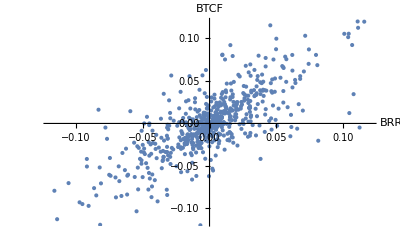

```mathematica
p=ListPlot[{rbrr,rbtc}ᵀ, PlotStyle->Thick,AxesLabel->{"BRR", "BTCF"}]
```

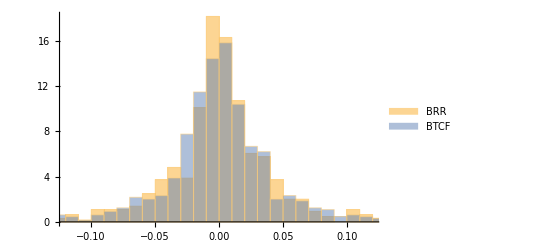

```mathematica
p=Histogram[{rbrr,rbtc}, Automatic, "PDF",ChartLegends->{"BRR", "BTCF"}]
```

```mathematica
Drbrr=EmpiricalDistribution[rbrr];
Drbtc=EmpiricalDistribution[rbtc];
```

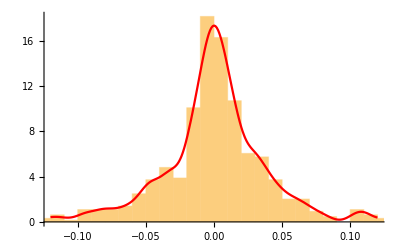
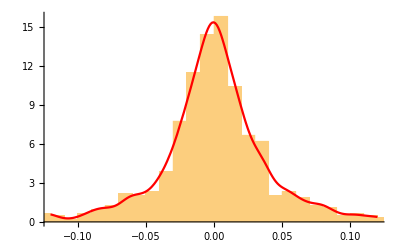

```mathematica
{p1=Show[
Histogram[rbrr, Automatic, "PDF"],
Plot[PDF[SmoothKernelDistribution[rbrr], x], {x,-0.12, 0.12},PlotStyle->Red]
],
p2=Show[
Histogram[rbtc, Automatic, "PDF"],
Plot[PDF[SmoothKernelDistribution[rbtc], x], {x,-0.12, 0.12},PlotStyle->Red]
]
}
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/rbrr.pdf",p1]
Export[NotebookDirectory[] <> "../latex/_pics/rbtc.pdf",p2]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/rbrr.pdf

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/rbtc.pdf

Make margins uniform

```mathematica
u=Table[CDF[Drbrr, rbrr[[i]]], {i,1,Length[rbrr]}];
v=Table[CDF[Drbtc, rbtc[[i]]], {i,1, Length[rbtc]}];
```

Drop largest sample (which has CDF of 1, messing up any sample mean-like computations)

```mathematica
u=DeleteCases[u, Max[u]];
v=DeleteCases[v, Max[v]];
```

Empirical copula

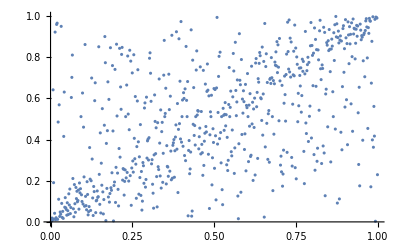

```mathematica
ListPlot[{u,v}ᵀ]
```

-Graphics-

```mathematica
μhat[u_,r_,α_,β_]:=Mean[NIGInv[u,α,β]^r]
```

```mathematica
NIGInv[0.9,1,0]
```

1.13899

```mathematica
Timing[Table[μhat[u,r,2,0], {r,3,4}]]
```

{14.3466,{-3.60347×10^-13,3.21827}}

```mathematica
Timing[Table[μhat[u,r,1,0], {r,3,4}]]
```

{15.3363,{-8.11034×10^-13,4.33998}}

```mathematica
Timing[Table[μhat[u,r,1,-0.5], {r,3,4}]]
```

{12.1558,{-1.45443,7.68684}}

```mathematica
D[M[u0,α,β,μ[α,β],δ[α,β]],{u0,3}]/.{u0->0,α->1,β->-0.5}
```

-2.

```mathematica
D[M[u0,α,β,μ[α,β],δ[α,β]],{u0,4}]/.{u0->0,α->1,β->-0.5}
```

13.6667

```mathematica
38./25
```

1.52

```mathematica
1.1296 + 1.52^2
```

3.44

```mathematica
M[u,
```